# HW 30 Problem 4

```mathematica
mu=0;
f[q_]:=1/(Exp[(e-mu)/kbT]+q)
```

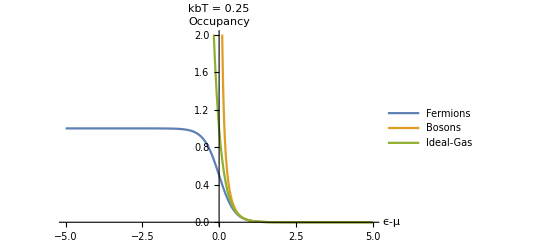

```mathematica
kbT=0.25;
Plot[{f[1],f[-1],f[0]},{e,mu-5,mu+5},PlotRange->{0,2},PlotLegends->{"Fermions","Bosons","Ideal-Gas"},AxesLabel->{ ϵ-μ,Occupancy},PlotLabel->"kbT = 0.25"]
```

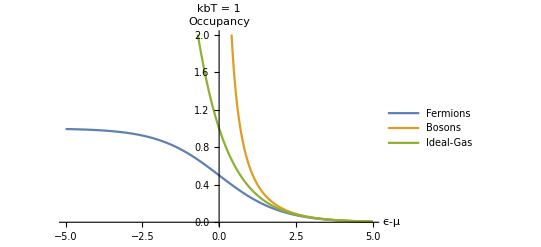

```mathematica
kbT=1;
Plot[{f[1],f[-1],f[0]},{e,mu-5,mu+5},PlotRange->{0,2},PlotLegends->{"Fermions","Bosons","Ideal-Gas"},AxesLabel->{ ϵ-μ,Occupancy},PlotLabel->"kbT = 1"]
```

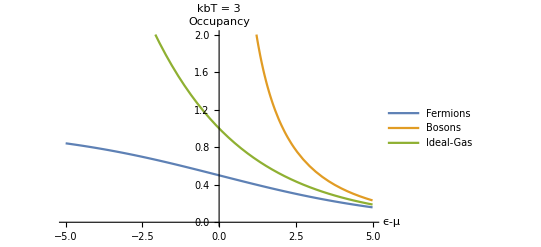

```mathematica
kbT=3;
Plot[{f[1],f[-1],f[0]},{e,mu-5,mu+5},PlotRange->{0,2},PlotLegends->{"Fermions","Bosons","Ideal-Gas"},AxesLabel->{ ϵ-μ,Occupancy},PlotLabel->"kbT = 3"]
```

```mathematica
(* Interpret the results *)
```

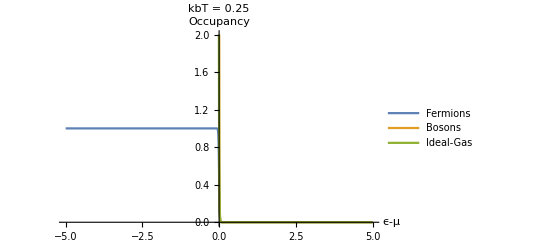

```mathematica
kbT=0.01;
Plot[{f[1],f[-1],f[0]},{e,mu-5,mu+5},PlotRange->{0,2},PlotLegends->{"Fermions","Bosons","Ideal-Gas"},AxesLabel->{ ϵ-μ,Occupancy},PlotLabel->"kbT = 0.25"]
```

As you can see, as T approaches 0, the three distributions take much 
starker steps. The Fermi-Dirac distribution (the one in blue) essentially becomes a step function, staying on at -1 for all negative numbers and then turning off at zero. The Bose-Einstein distribution shoots upwards at the zero mark and remains 0 for all positive e - u. The classical single-state occupancy distribution does something similar. It shoots up at 0, but remains 0 for any positive e - u.